```mathematica
(**********************************************)
(*******Generate plot in Figure S7B, Left****************) 
(**********************************************)
```

```mathematica
(***From Ai9 injections***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
mouseList={"Mouse21196","Mouse21180","Mouse22447","Mouse21185","Mouse21137","Mouse21200","Mouse22448","Mouse21177","Mouse21197","Mouse22439"};
```

```mathematica
normCellCountsV1=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/Ai9/",mouseList[[n]],"/",mouseList[[n]],"_RH_V1_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLP=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/Ai9/",mouseList[[n]],"/",mouseList[[n]],"_RH_LP_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLM=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/Ai9/",mouseList[[n]],"/",mouseList[[n]],"_RH_LM_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
(***)
```

```mathematica
xValsV1=Mean[normCellCountsV1][[All,1]];
```

```mathematica
meanNormCellCountsV1=Mean[normCellCountsV1][[All,2]];
```

```mathematica
semNormCellCountsV1=StandardDeviation[normCellCountsV1][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g1=ListLinePlot[{Partition[Riffle[xValsV1,meanNormCellCountsV1],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1+semNormCellCountsV1)],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1-semNormCellCountsV1)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]}},PlotStyle->{{v1Color,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLP=Mean[normCellCountsLP][[All,1]];
```

```mathematica
meanNormCellCountsLP=Mean[normCellCountsLP][[All,2]];
```

```mathematica
semNormCellCountsLP=StandardDeviation[normCellCountsLP][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g2=ListLinePlot[{Partition[Riffle[xValsLP,meanNormCellCountsLP],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP+semNormCellCountsLP)],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP-semNormCellCountsLP)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lpColor]},1->{{3},Directive[Opacity[0.2],lpColor]}},PlotStyle->{{lpColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLM=Mean[normCellCountsLM][[All,1]];
```

```mathematica
meanNormCellCountsLM=Mean[normCellCountsLM][[All,2]];
```

```mathematica
semNormCellCountsLM=StandardDeviation[normCellCountsLM][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g3=ListLinePlot[{Partition[Riffle[xValsLM,meanNormCellCountsLM],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM+semNormCellCountsLM)],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM-semNormCellCountsLM)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lmColor]},1->{{3},Directive[Opacity[0.2],lmColor]}},PlotStyle->{{lmColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[-0.1,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

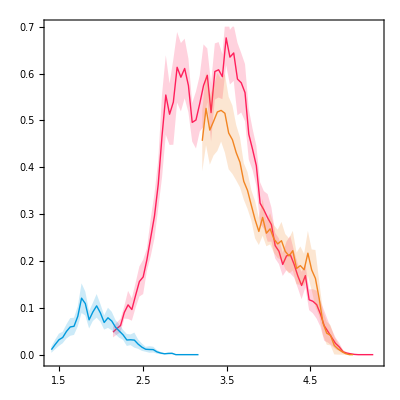

```mathematica
Show[g1,g2,g3]
```

```mathematica
(**********************************************)
(*******Generate plot in Figure S7B, Right****************) 
(**********************************************)
```

```mathematica
(***From eOPN3 injections***)
```

```mathematica
mouseList={"Mouse493","Mouse494","Mouse500"};
```

```mathematica
normCellCountsV1=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/eOPN3/",mouseList[[n]],"/",mouseList[[n]],"_V1NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLP=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/eOPN3/",mouseList[[n]],"/",mouseList[[n]],"_LPNormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLM=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS7/FigS7Data/eOPN3/",mouseList[[n]],"/",mouseList[[n]],"_LMNormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
(***)
```

```mathematica
xValsV1=Mean[normCellCountsV1][[All,1]];
```

```mathematica
meanNormCellCountsV1=Mean[normCellCountsV1][[All,2]];
```

```mathematica
semNormCellCountsV1=StandardDeviation[normCellCountsV1][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g1=ListLinePlot[{Partition[Riffle[xValsV1,meanNormCellCountsV1],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1+semNormCellCountsV1)],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1-semNormCellCountsV1)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]}},PlotStyle->{{v1Color,Thick,Dashed},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLP=Mean[normCellCountsLP][[All,1]];
```

```mathematica
meanNormCellCountsLP=Mean[normCellCountsLP][[All,2]];
```

```mathematica
semNormCellCountsLP=StandardDeviation[normCellCountsLP][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g2=ListLinePlot[{Partition[Riffle[xValsLP,meanNormCellCountsLP],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP+semNormCellCountsLP)],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP-semNormCellCountsLP)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lpColor]},1->{{3},Directive[Opacity[0.2],lpColor]}},PlotStyle->{{lpColor,Thick,Dashed},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLM=Mean[normCellCountsLM][[All,1]];
```

```mathematica
meanNormCellCountsLM=Mean[normCellCountsLM][[All,2]];
```

```mathematica
semNormCellCountsLM=StandardDeviation[normCellCountsLM][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g3=ListLinePlot[{Partition[Riffle[xValsLM,meanNormCellCountsLM],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM+semNormCellCountsLM)],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM-semNormCellCountsLM)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lmColor]},1->{{3},Directive[Opacity[0.2],lmColor]}},PlotStyle->{{lmColor,Thick,Dashed},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[-0.1,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

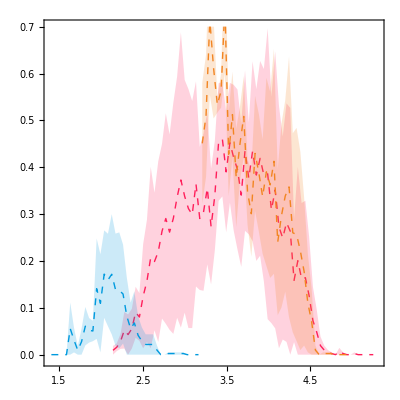

```mathematica
Show[g1,g2,g3]
```